Analisi dei modi naturali e risposta libera per un sistema con tre stati a tempo discreto

```mathematica
A=({{-1/6, 0, 0}, {1/4-(√5)/16, -1/2+(√5)/16, 1/4-(√5)/16}, {5/12-(5 √5)/16, -3/2+(5 √5)/16, 1/4-(5 √5)/16}})
```

{{-1/6,0,0},{1/4-(√5)/16,-1/2+(√5)/16,1/4-(√5)/16},{5/12-(5 √5)/16,-3/2+(5 √5)/16,1/4-(5 √5)/16}}

Mi calcolo gli autovalori di A

```mathematica
Eigenvalues[A]
```

{1/8 (-1-√5+ⅈ √(10-2 √5)),1/8 (-1-√5-ⅈ √(10-2 √5)),-1/6}

Notiamo che la successione (modo naturale) legata all’autovalore reale posizionato in -1/6 e’ un modo pseudo-oscillatorio

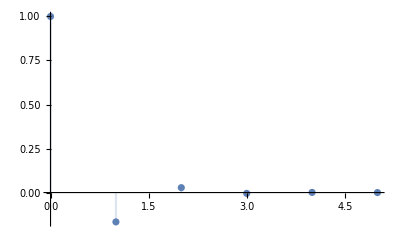

```mathematica
DiscretePlot[(-1/6)^k,{k,0,5},PlotRange->All]
```

Mi calcolo ora il modulo e la fase degli autovalori complessi e coniugati di A

```mathematica
ρ=Simplify[Abs[Eigenvalues[A][[1]]]]
```

1/2

```mathematica
θ=Simplify[Arg[Eigenvalues[A][[1]]]]
```

(4 π)/5

Verifico la periodicita’ della componente trigonometrica dei modi naturali

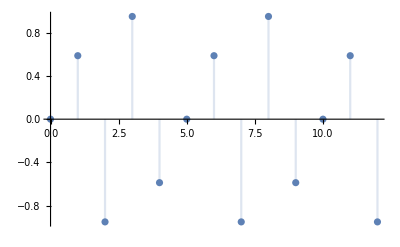

```mathematica
DiscretePlot[Sin[4/5 π k],{k,0,12}]
```

Determino la matrice di cambiamento di base, tenendo conto che gli autovalori sono complessi e coniugati

```mathematica
T=Transpose[Eigenvectors[A]]
```

{{0,0,-1},{-(6-3 √5-2 ⅈ √(2 (5-√5)))/(-24+5 √5),-(6-3 √5+2 ⅈ √(2 (5-√5)))/(-24+5 √5),0},{1,1,1}}

```mathematica
MatrixForm[T]
```

(0 | 0 | -1
-(6-3 √5-2 ⅈ √(2 (5-√5)))/(-24+5 √5) | -(6-3 √5+2 ⅈ √(2 (5-√5)))/(-24+5 √5) | 0
1 | 1 | 1)

poiche’ gli autovalori sono complessi e coniugati mi costruisco la matrice di cambiamento di base nella forma canonica scaling-rotation

```mathematica
T̃=Transpose[{Re[T[[All,1]]],Im[T[[All,1]]],T[[All,3]]}]
```

{{0,0,-1},{-(6-3 √5)/(-24+5 √5),(2 √(2 (5-√5)))/(-24+5 √5),0},{1,0,1}}

```mathematica
MatrixForm[T̃]
```

(0 | 0 | -1
-(6-3 √5)/(-24+5 √5) | (2 √(2 (5-√5)))/(-24+5 √5) | 0
1 | 0 | 1)

Verifico che la matrice simile ad A mediante la matrice di cambiamento di base e’ in forma diagonale a blocchi

```mathematica
Ã=Simplify[Inverse[T̃].A.T̃]
```

{{1/8 (-1-√5),1/4 √(1/2 (5-√5)),0},{(-5+√5)/(4 √(10-2 √5)),1/8 (-1-√5),0},{0,0,-1/6}}

```mathematica
MatrixForm[Ã]
```

(1/8 (-1-√5) | 1/4 √(1/2 (5-√5)) | 0
(-5+√5)/(4 √(10-2 √5)) | 1/8 (-1-√5) | 0
0 | 0 | -1/6)

Inserisco lo stato iniziale e lo proietto lungo le colonne della matrice di cambiamento di base

```mathematica
Subscript[x, 0]=({{1}, {0}, {0}})
```

{{1},{0},{0}}

```mathematica
Subscript[z, 0]=Simplify[Inverse[T̃].Subscript[x, 0]]
```

{{1},{-(3 (-2+√5))/(2 √(10-2 √5))},{-1}}

```mathematica
MatrixForm[Subscript[z, 0]]
```

(1
-(3 (-2+√5))/(2 √(10-2 √5))
-1)

Scrivo ora la risposta libera

```mathematica
Subscript[x, l][k_]:=T̃.({{ρ^k Cos[θ k], ρ^k Sin[θ k], 0}, {-ρ^k Sin[θ k], ρ^k Cos[θ k], 0}, {0, 0, (-1/6)^k}}).Subscript[z, 0]
```

Grafico della risposta libera

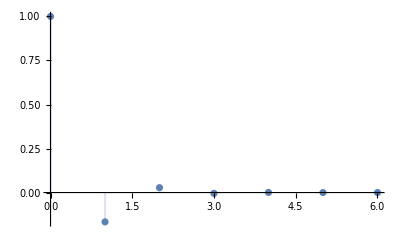

```mathematica
DiscretePlot[Subscript[x, l][k][[1]],{k,0,6},PlotRange->All]
```

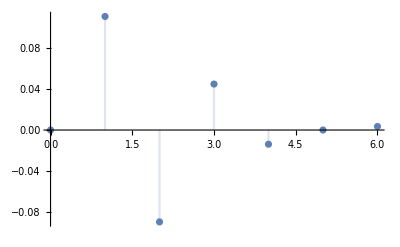

```mathematica
DiscretePlot[Subscript[x, l][k][[2]],{k,0,6},PlotRange->All]
```

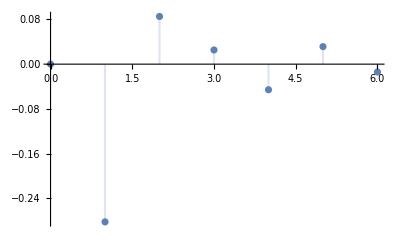

```mathematica
DiscretePlot[Subscript[x, l][k][[3]],{k,0,6},PlotRange->All]
```

```mathematica
MatrixForm[T̃]
```

(0 | 0 | -1
-(6-3 √5)/(-24+5 √5) | (2 √(2 (5-√5)))/(-24+5 √5) | 0
1 | 0 | 1)

Considero ora il seguente stato iniziale

```mathematica
Subscript[x, 0]=({{5}, {0}, {-5}})
```

{{5},{0},{-5}}

```mathematica
Subscript[z, 0]=Simplify[Inverse[T̃].Subscript[x, 0]]
```

{{0},{0},{-5}}

```mathematica
Subscript[x, l][k_]:=T̃.({{ρ^k Cos[θ k], ρ^k Sin[θ k], 0}, {-ρ^k Sin[θ k], ρ^k Cos[θ k], 0}, {0, 0, (-1/6)^k}}).Subscript[z, 0]
```

```mathematica
Subscript[x, l][k]
```

{{5 (-1/6)^k},{0},{-5 (-1/6)^k}}

```mathematica
MatrixForm[Subscript[x, l][k]]
```

(5 (-1/6)^k
0
-5 (-1/6)^k)

```mathematica
Subscript[x, 0]=({{1}, {0}, {0}})
```

{{1},{0},{0}}

```mathematica
Subscript[z, 0]=Simplify[Inverse[T̃].Subscript[x, 0]]
```

{{1},{-(3 (-2+√5))/(2 √(10-2 √5))},{-1}}

```mathematica
Subscript[x, l][k_]:=T̃.({{ρ^k Cos[θ k], ρ^k Sin[θ k], 0}, {-ρ^k Sin[θ k], ρ^k Cos[θ k], 0}, {0, 0, (-1/6)^k}}).Subscript[z, 0]
```

```mathematica
MatrixForm[T̃]
```

(0 | 0 | -1
-(6-3 √5)/(-24+5 √5) | (2 √(2 (5-√5)))/(-24+5 √5) | 0
1 | 0 | 1)

Se non voglio “vedere” sull’uscita il terzo modo naturale devo selezionare C in maniera tale che C t_3 = 0

```mathematica
Cc=({{1, 0, 1}})
```

{{1,0,1}}

```mathematica
Subscript[y, l][k_]:=Cc.Subscript[x, l][k]
```

```mathematica
Subscript[y, l][k]
```

{{2^-k Cos[(4 k π)/5]-(3 2^(-1-k) (-2+√5) Sin[(4 k π)/5])/(√(10-2 √5))}}

Se voglio “vedere” sull’uscita “solo” il terzo modo naturale devo selezionare C in maniera tale che C t_1 = 0 e C t_2 = 0

```mathematica
Cc=({{1, 0, 0}})
```

{{1,0,0}}

```mathematica
Subscript[y, l][k_]:=Cc.Subscript[x, l][k]
```

```mathematica
Subscript[y, l][k]
```

{{(-1/6)^k}}